## Bounds on EDGB Theory From the Overall Posterior of GW150914

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"];(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-phase-only-beta.csv","CSV"] ;(*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-amp-only-alpha.csv","CSV"]; (*PPE alpha*)
```

```mathematica
dataOverall4=Import[NotebookDirectory[]<>"/-1pn-combined-correlated-beta.csv","CSV"]; (*PPE beta for phase and amp combined*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
DL=dataOverall1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,16318,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,16317,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1All=dataOverall1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 (*Ligo posterior gives mass in detector frame*);
m2All=dataOverall1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,16318,0.000135998,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1.64485*dataOverall2[[All,1]](*90% upper bound*)
αppEAll=1.64485*dataOverall3[[All,1]](*90% upper bound*)
```

{0.00013746,0.000141116,0.000145804,0.00013958,0.000137616,0.000161825,0.000141987,16318,0.000144633,0.000145378,0.000144348,0.000143774,0.000155917,0.000154399,0.000146727}
 |  |  |  |

{0.0266405,0.0276385,0.0260987,0.0274961,0.0265455,0.0253835,0.0282802,16318,0.0260638,0.0266036,0.0263939,0.0264988,0.0262784,0.0258012,0.0274642}
 |  |  |  |

```mathematica
βppEComb=1.64485*dataOverall4[[All,1]](*90% upper bound*)
```

{0.000148781,0.000153264,0.000157738,0.000151464,0.000149043,0.000174137,0.000154263,16318,0.000156383,0.00015756,0.000156255,0.000155505,0.000168333,0.000167073,0.000159236}
 |  |  |  |

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] (*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*)
```

{0.748761,0.163456,0.0531362,438.938,2.13954,0.0203166,2.21675,0.111597,16316,0.371072,0.0535842,0.0896465,0.0995473,0.110349,0.0180631,0.0334412,0.158835}
 |  |  |  |

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll](*Sigma_Zeta from amplitude corrections*)
```

{3.887,0.857518,0.254767,2316.08,11.0546,0.085361,11.8265,0.540324,16316,1.78754,0.258649,0.439418,0.487556,0.544775,0.0815459,0.149686,0.796353}
 |  |  |  |

```mathematica
ζcombAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEComb]
```

{0.81043,0.177527,0.057485,476.307,2.3172,0.0218623,2.40842,0.120596,16316,0.402289,0.0579374,0.0971583,0.107759,0.119352,0.0195016,0.0361863,0.172375}
 |  |  |  |

```mathematica
Length[m1All]
```

16332

```mathematica
Length[βppEAll]
```

16332

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

11390

```mathematica
Length[ζAllampSelected]
```

6261

```mathematica
Mean[ζAllphaseSelected]
```

0.257895

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.233642

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.851562},{1},16329,{-0.960167,432.955,7,0.304489,0.180842}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.851562,4.42067},16330,{-0.960167,432.955,8,0.180842,0.906687}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] ;(*Data satisfying zeta_phase<1*)
```

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{-0.835255,614.169,2.3996,-1.15619,39.5694,34.4793,0.70691,0.434739,-0.100755,0.415459,0.188078,0.986691},6259,{-0.960167,432.955,8,0.180842,0.906687}}
 |  |  |  |

```mathematica
A4[[All,12]];
```

```mathematica
Length[A3]
```

11390

```mathematica
Length[A4]
```

6261

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.470722

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{50.3771,34.9861,25.6762,260.139,64.3169,20.9237,71.236,30.1544,16316,43.8442,25.5242,30.3292,30.0617,31.5047,19.8146,23.5044,35.7419}
 |  |  |  |

{33.3745,23.1172,17.3517,171.64,42.6599,14.6146,46.8721,20.3283,16316,29.5946,17.22,20.3833,20.2076,21.1355,13.5936,16.1594,23.8857}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBphase]
```

38.0448

```mathematica
StandardDeviation[SqrtαEDGBphase]
```

55.464

```mathematica
SqrtαEDGBcomb=((ζcombAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{34.0415,23.5994,17.6963,175.182,43.5191,14.8849,47.854,20.7263,16316,30.1983,17.5596,20.7975,20.612,21.554,13.8565,16.4812,24.3793}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

59.2173

```mathematica
Mean[SqrtαEDGBphase]
```

39.305

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

```mathematica
Mean[SqrtαEDGBphaseSelected]
```

21.6435

```mathematica
Mean[SqrtαEDGBampSelected]
```

32.1641

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{14.0312,12.5623,11.4148,20.5816,15.013,10.7281,15.3897,12.0481,16316,13.5504,11.3843,12.0589,12.0242,12.2038,10.4384,11.13,12.6931}
 |  |  |  |

```mathematica
MaxLogSquaredαPhase=Max[LogSquaredαPhase]
```

32.3757

```mathematica
MinLogSquaredαPhase=Min[LogSquaredαPhase]
```

9.53088

```mathematica
𝒟logα=HistogramDistribution[LogSquaredαPhase] ;
```

```mathematica
pslogαPhase=PDF[𝒟logα,x];
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,15,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αPhaseMC[x_]=pslogαPhase;
```

```mathematica
αPhaseMC[4]
```

0.

```mathematica
αPhaseMC[33]
```

0.

```mathematica
αMCSample=Range[3.5,35,1];
```

```mathematica
αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterp=Interpolation[αMCTable];
```

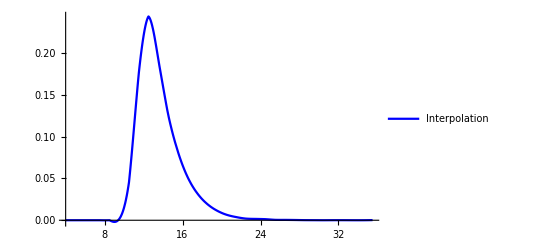

```mathematica
plotαMCTableInterp=Plot[αMCTableInterp[x],{x,4,35.5},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

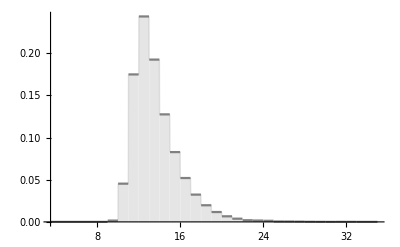

```mathematica
plot5=Plot[αPhaseMC[x],{x,3.5,35},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

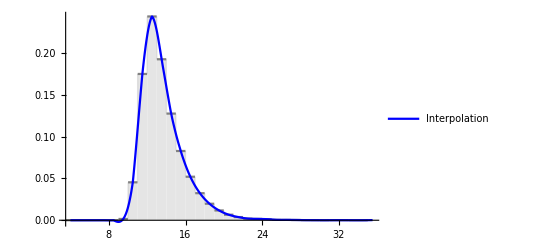

```mathematica
Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]αMCTableInterp[y],{y,MinLogSquaredαPhase,MaxLogSquaredαPhase}]},{i,1,Length[fun1αphaseTable[y]]}]
```

{{0,1.78411×10^-6},{1.×10^-7,1.78411×10^-6},{1.25893×10^-7,1.78411×10^-6},{1.58489×10^-7,1.78411×10^-6},{1.99526×10^-7,1.78411×10^-6},{2.51189×10^-7,1.78411×10^-6},{3.16228×10^-7,1.78411×10^-6},{3.98107×10^-7,1.78411×10^-6},{5.01187×10^-7,1.78411×10^-6},{6.30957×10^-7,1.78411×10^-6},{7.94328×10^-7,1.78411×10^-6},{1.×10^-6,1.78411×10^-6},{1.25893×10^-6,1.78411×10^-6},{1.58489×10^-6,1.78411×10^-6},{1.99526×10^-6,1.78411×10^-6},{2.51189×10^-6,1.78411×10^-6},{3.16228×10^-6,1.78411×10^-6},{3.98107×10^-6,1.78411×10^-6},{5.01187×10^-6,1.78411×10^-6},{6.30957×10^-6,1.78411×10^-6},{7.94328×10^-6,1.78411×10^-6},{0.00001,1.78411×10^-6},{0.0000125893,1.78411×10^-6},{0.0000158489,1.78411×10^-6},{0.0000199526,1.78411×10^-6},{0.0000251189,1.78411×10^-6},{0.0000316228,1.78411×10^-6},{0.0000398107,1.78411×10^-6},{0.0000501187,1.78411×10^-6},{0.0000630957,1.78411×10^-6},{0.0000794328,1.78411×10^-6},{0.0001,1.78411×10^-6},{0.000125893,1.78411×10^-6},{0.000158489,1.78411×10^-6},{0.000199526,1.78411×10^-6},{0.000251189,1.78411×10^-6},{0.000316228,1.78411×10^-6},{0.000398107,1.78411×10^-6},{0.000501187,1.78411×10^-6},{0.000630957,1.78411×10^-6},{0.000794328,1.78411×10^-6},{0.001,1.78411×10^-6},{0.00125893,1.78411×10^-6},{0.00158489,1.78411×10^-6},{0.00199526,1.78411×10^-6},{0.00251189,1.78411×10^-6},{0.00316228,1.78411×10^-6},{0.00398107,1.78411×10^-6},{0.00501187,1.78411×10^-6},{0.00630957,1.78411×10^-6},{0.00794328,1.78411×10^-6},{0.01,1.78411×10^-6},{0.0125893,1.78411×10^-6},{0.0158489,1.78411×10^-6},{0.0199526,1.78411×10^-6},{0.0251189,1.78411×10^-6},{0.0316228,1.78411×10^-6},{0.0398107,1.78411×10^-6},{0.0501187,1.78411×10^-6},{0.0630957,1.78411×10^-6},{0.0794328,1.78411×10^-6},{0.1,1.78411×10^-6},{0.125893,1.78411×10^-6},{0.158489,1.78411×10^-6},{0.199526,1.78411×10^-6},{0.251189,1.78411×10^-6},{0.316228,1.78411×10^-6},{0.398107,1.78411×10^-6},{0.501187,1.78411×10^-6},{0.630957,1.78411×10^-6},{0.794328,1.78411×10^-6},{1.,1.78411×10^-6},{1.25893,1.78411×10^-6},{1.58489,1.78411×10^-6},{1.99526,1.78411×10^-6},{2.51189,1.78411×10^-6},{3.16228,1.78411×10^-6},{3.98107,1.78411×10^-6},{5.01187,1.78411×10^-6},{6.30957,1.78411×10^-6},{7.94328,1.78411×10^-6},{10.,1.78411×10^-6},{12.5893,1.78411×10^-6},{15.8489,1.78411×10^-6},{19.9526,1.78411×10^-6},{25.1189,1.78411×10^-6},{31.6228,1.78411×10^-6},{39.8107,1.78411×10^-6},{50.1187,1.78411×10^-6},{63.0957,1.78411×10^-6},{79.4328,1.78411×10^-6},{100.,1.7841×10^-6},{125.893,1.7841×10^-6},{158.489,1.7841×10^-6},{199.526,1.78409×10^-6},{251.189,1.78409×10^-6},{316.228,1.78407×10^-6},{398.107,1.78405×10^-6},{501.187,1.78402×10^-6},{630.957,1.78396×10^-6},{794.328,1.78388×10^-6},{1000.,1.78375×10^-6},{1258.93,1.78353×10^-6},{1584.89,1.7832×10^-6},{1995.26,1.78267×10^-6},{2511.89,1.78183×10^-6},{3162.28,1.7805×10^-6},{3981.07,1.77841×10^-6},{5011.87,1.77511×10^-6},{6309.57,1.76993×10^-6},{7943.28,1.76184×10^-6},{10000.,1.74934×10^-6},{12589.3,1.73025×10^-6},{15848.9,1.70167×10^-6},{19952.6,1.66014×10^-6},{25118.9,1.6021×10^-6},{31622.8,1.52499×10^-6},{39810.7,1.42822×10^-6},{50118.7,1.31342×10^-6},{63095.7,1.18392×10^-6},{79432.8,1.04437×10^-6},{100000.,9.00582×10^-7},{125893.,7.59008×10^-7},{158489.,6.25634×10^-7},{199526.,5.04933×10^-7},{251189.,3.99507×10^-7},{316228.,3.10259×10^-7},{398107.,2.36809×10^-7},{501187.,1.77946×10^-7},{630957.,1.31959×10^-7},{794328.,9.68502×10^-8},{1.×10^6,7.05454×10^-8},{1.25893×10^6,5.11072×10^-8},{1.58489×10^6,3.68814×10^-8},{1.99526×10^6,2.65402×10^-8},{2.51189×10^6,1.90608×10^-8},{3.16228×10^6,1.36727×10^-8},{3.98107×10^6,9.80059×10^-9},{5.01187×10^6,7.02014×10^-9},{6.30957×10^6,5.02346×10^-9},{7.94328×10^6,3.59016×10^-9},{1.×10^7,2.56251×10^-9},{1.25893×10^7,1.82687×10^-9},{1.58489×10^7,1.30112×10^-9},{1.99526×10^7,9.25905×10^-10},{2.51189×10^7,6.58399×10^-10},{3.16228×10^7,4.67825×10^-10},{3.98107×10^7,3.32127×10^-10},{5.01187×10^7,2.35551×10^-10},{6.30957×10^7,1.66862×10^-10},{7.94328×10^7,1.18049×10^-10},{1.×10^8,8.34005×10^-11},{1.25893×10^8,5.88358×10^-11},{1.58489×10^8,4.14424×10^-11},{1.99526×10^8,2.91432×10^-11},{2.51189×10^8,2.04593×10^-11},{3.16228×10^8,1.43386×10^-11},{3.98107×10^8,1.00326×10^-11},{5.01187×10^8,7.00949×10^-12},{6.30957×10^8,4.89183×10^-12},{7.94328×10^8,3.41183×10^-12},{1.×10^9,2.37947×10^-12},{1.25893×10^9,1.66015×10^-12},{1.58489×10^9,1.15906×10^-12},{1.99526×10^9,8.09891×10^-13},{2.51189×10^9,5.66555×10^-13},{3.16228×10^9,3.97145×10^-13},{3.98107×10^9,2.79505×10^-13},{5.01187×10^9,1.98104×10^-13},{6.30957×10^9,1.41899×10^-13},{7.94328×10^9,1.02975×10^-13},{1.×10^10,7.57036×10^-14},{1.25893×10^10,5.62065×10^-14},{1.58489×10^10,4.19151×10^-14},{1.99526×10^10,3.12019×10^-14},{2.51189×10^10,2.30596×10^-14},{3.16228×10^10,1.68489×10^-14},{3.98107×10^10,1.21357×10^-14},{5.01187×10^10,8.60193×10^-15},{6.30957×10^10,5.99958×10^-15},{7.94328×10^10,4.12862×10^-15},{1.×10^11,2.82304×10^-15},{1.25893×10^11,1.94016×10^-15},{1.58489×10^11,1.35692×10^-15},{1.99526×10^11,9.72888×10^-16},{2.51189×10^11,7.1363×10^-16},{3.16228×10^11,5.29875×10^-16},{3.98107×10^11,3.92985×10^-16},{5.01187×10^11,2.88151×10^-16},{6.30957×10^11,2.07698×10^-16},{7.94328×10^11,1.46851×10^-16},{1.×10^12,1.01841×10^-16},{1.25893×10^12,6.93031×10^-17},{1.58489×10^12,4.63135×10^-17},{1.99526×10^12,3.04689×10^-17},{2.51189×10^12,1.98351×10^-17},{3.16228×10^12,1.287×10^-17},{3.98107×10^12,8.3827×10^-18},{5.01187×10^12,5.50394×10^-18},{6.30957×10^12,3.64294×10^-18},{7.94328×10^12,2.42872×10^-18},{1.×10^13,1.64072×10^-18},{1.25893×10^13,1.14392×10^-18},{1.58489×10^13,8.45753×10^-19},{1.99526×10^13,6.74669×10^-19},{2.51189×10^13,5.73343×10^-19},{3.16228×10^13,4.99931×10^-19},{3.98107×10^13,4.29649×10^-19},{5.01187×10^13,3.53187×10^-19},{6.30957×10^13,2.72389×10^-19},{7.94328×10^13,1.94304×10^-19},{1.×10^14,1.26131×10^-19},{1.25893×10^14,7.26823×10^-20},{1.58489×10^14,3.56774×10^-20},{1.99526×10^14,1.39152×10^-20},{2.51189×10^14,3.84355×10^-21},{3.16228×10^14,6.24248×10^-22},{3.98107×10^14,4.42748×10^-23},{5.01187×10^14,8.53462×10^-25},{6.30957×10^14,2.10337×10^-27},{7.94328×10^14,2.00121×10^-31},{1.×10^15,1.09983×10^-37}}

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog];
```

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^15}]
```

0.499991

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

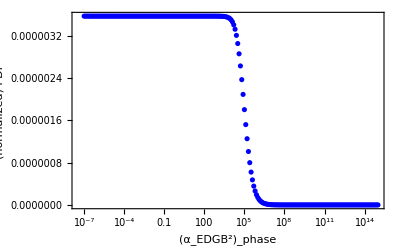

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLinearPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm];
```

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

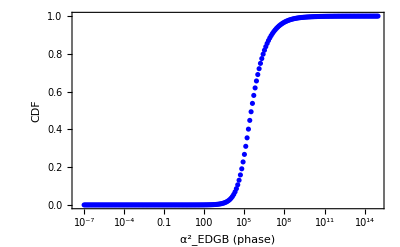

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm];
```

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

1.06323×10^7

```mathematica
√√αSquared90CLphase//N   (*90% CL upper bound*)
```

57.1028

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{15.6781,14.2198,12.9823,22.2449,16.6553,12.1635,17.064,13.6253,16316,15.1226,12.9585,13.6484,13.613,13.8005,11.9457,12.6287,14.3053}
 |  |  |  |

```mathematica
MaxLogSquaredαamp=Max[LogSquaredαamp]
```

34.0444

```mathematica
MinLogSquaredαamp=Min[LogSquaredαamp]
```

11.0626

```mathematica
𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;
```

```mathematica
pslogαamp=PDF[𝒟logαamp,x];
```

```mathematica
Histogram[LogSquaredαamp];
```

```mathematica
αampMC[x_]=pslogαamp;
```

```mathematica
αampMC[35]
```

0.

```mathematica
αampMC[5]
```

0.

```mathematica
αMCSampleamp=Range[5,35,1.2];
```

```mathematica
αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];
```

```mathematica
αMCTableInterpamp=Interpolation[αMCTableamp];
```

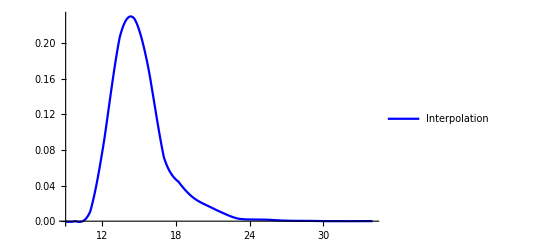

```mathematica
plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,9,34},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

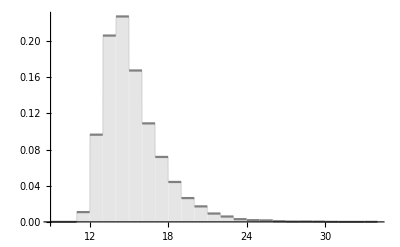

```mathematica
plot6=Plot[αampMC[x],{x,9,34},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

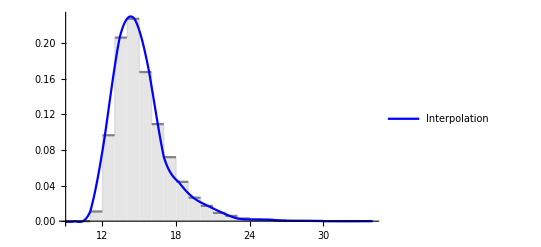

```mathematica
Show[plot6,plotαMCTableInterpamp]
```

```mathematica
αSampleLogamp=Prepend[10^Range[-7,15,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]αMCTableInterpamp[y],{y,MinLogSquaredαamp,MaxLogSquaredαPhase}]},{i,1,Length[fun1αampTable[y]]}];
```

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,10^15}]
```

0.528966

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

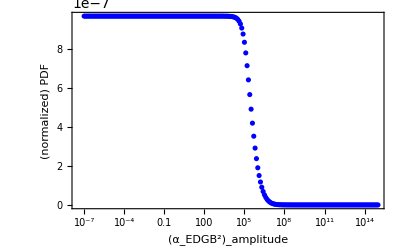

```mathematica
plotαFinalPDFampLogNorm=ListLogLinearPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

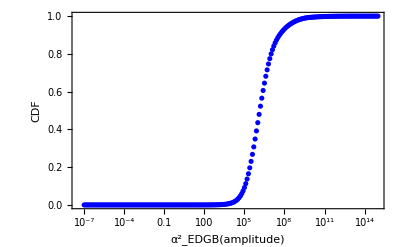

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

4.24229×10^7

```mathematica
√√αSquared90CLamp
```

80.7049

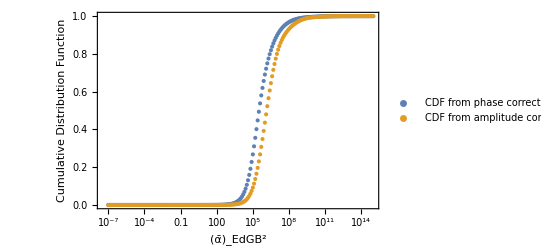

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True] (*Shows that indeed for GW150914, the amplitude and phase corrections are comparable*)
```

Combined Correction

```mathematica
LogSquaredαcomb=Log[SqrtαEDGBcomb^4] (*This is Log of sigma_(alpha^2)*)
```

{14.1103,12.6449,11.4934,20.6633,15.0928,10.8014,15.4726,12.1256,16316,13.6311,11.4624,12.1393,12.1035,12.2822,10.515,11.2089,12.7749}
 |  |  |  |

```mathematica
MaxLogSquaredαcomb=Max[LogSquaredαcomb]
```

32.4567

```mathematica
MinLogSquaredαcomb=Min[LogSquaredαcomb]
```

9.58267

```mathematica
𝒟logαcomb=HistogramDistribution[LogSquaredαcomb] ;
```

```mathematica
pslogαcomb=PDF[𝒟logαcomb,x];
```

```mathematica
Histogram[LogSquaredαcomb];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,15,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αcombTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αcombMC[x_]=pslogαcomb;
```

```mathematica
αcombMC[4]
```

0.

```mathematica
αcombMC[33]
```

0.

```mathematica
αMCSample=Range[3.5,35,1];
```

```mathematica
αMCTablecomb=Table[{αMCSample[[i]],αcombMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterpcomb=Interpolation[αMCTablecomb];
```

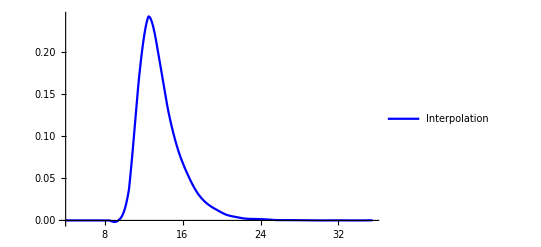

```mathematica
plotαMCTableInterpcomb=Plot[αMCTableInterpcomb[x],{x,4,35.5},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

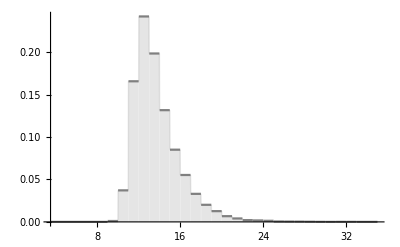

```mathematica
plot8=Plot[αcombMC[x],{x,3.5,35},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

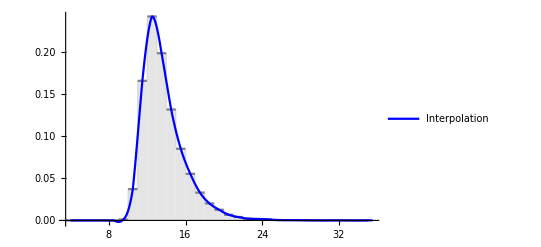

```mathematica
Show[plot8,plotαMCTableInterpcomb] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFcombLog=Table[{fun1αcombTable[y][[i,1]],NIntegrate[fun1αcombTable[y][[i,2]]αMCTableInterpcomb[y],{y,MinLogSquaredαcomb,MaxLogSquaredαcomb}]},{i,1,Length[fun1αcombTable[y]]}]
```

{{0,1.63893×10^-6},{1.×10^-7,1.63893×10^-6},{1.25893×10^-7,1.63893×10^-6},{1.58489×10^-7,1.63893×10^-6},{1.99526×10^-7,1.63893×10^-6},{2.51189×10^-7,1.63893×10^-6},{3.16228×10^-7,1.63893×10^-6},{3.98107×10^-7,1.63893×10^-6},{5.01187×10^-7,1.63893×10^-6},{6.30957×10^-7,1.63893×10^-6},{7.94328×10^-7,1.63893×10^-6},{1.×10^-6,1.63893×10^-6},{1.25893×10^-6,1.63893×10^-6},{1.58489×10^-6,1.63893×10^-6},{1.99526×10^-6,1.63893×10^-6},{2.51189×10^-6,1.63893×10^-6},{3.16228×10^-6,1.63893×10^-6},{3.98107×10^-6,1.63893×10^-6},{5.01187×10^-6,1.63893×10^-6},{6.30957×10^-6,1.63893×10^-6},{7.94328×10^-6,1.63893×10^-6},{0.00001,1.63893×10^-6},{0.0000125893,1.63893×10^-6},{0.0000158489,1.63893×10^-6},{0.0000199526,1.63893×10^-6},{0.0000251189,1.63893×10^-6},{0.0000316228,1.63893×10^-6},{0.0000398107,1.63893×10^-6},{0.0000501187,1.63893×10^-6},{0.0000630957,1.63893×10^-6},{0.0000794328,1.63893×10^-6},{0.0001,1.63893×10^-6},{0.000125893,1.63893×10^-6},{0.000158489,1.63893×10^-6},{0.000199526,1.63893×10^-6},{0.000251189,1.63893×10^-6},{0.000316228,1.63893×10^-6},{0.000398107,1.63893×10^-6},{0.000501187,1.63893×10^-6},{0.000630957,1.63893×10^-6},{0.000794328,1.63893×10^-6},{0.001,1.63893×10^-6},{0.00125893,1.63893×10^-6},{0.00158489,1.63893×10^-6},{0.00199526,1.63893×10^-6},{0.00251189,1.63893×10^-6},{0.00316228,1.63893×10^-6},{0.00398107,1.63893×10^-6},{0.00501187,1.63893×10^-6},{0.00630957,1.63893×10^-6},{0.00794328,1.63893×10^-6},{0.01,1.63893×10^-6},{0.0125893,1.63893×10^-6},{0.0158489,1.63893×10^-6},{0.0199526,1.63893×10^-6},{0.0251189,1.63893×10^-6},{0.0316228,1.63893×10^-6},{0.0398107,1.63893×10^-6},{0.0501187,1.63893×10^-6},{0.0630957,1.63893×10^-6},{0.0794328,1.63893×10^-6},{0.1,1.63893×10^-6},{0.125893,1.63893×10^-6},{0.158489,1.63893×10^-6},{0.199526,1.63893×10^-6},{0.251189,1.63893×10^-6},{0.316228,1.63893×10^-6},{0.398107,1.63893×10^-6},{0.501187,1.63893×10^-6},{0.630957,1.63893×10^-6},{0.794328,1.63893×10^-6},{1.,1.63893×10^-6},{1.25893,1.63893×10^-6},{1.58489,1.63893×10^-6},{1.99526,1.63893×10^-6},{2.51189,1.63893×10^-6},{3.16228,1.63893×10^-6},{3.98107,1.63893×10^-6},{5.01187,1.63893×10^-6},{6.30957,1.63893×10^-6},{7.94328,1.63893×10^-6},{10.,1.63893×10^-6},{12.5893,1.63893×10^-6},{15.8489,1.63893×10^-6},{19.9526,1.63893×10^-6},{25.1189,1.63893×10^-6},{31.6228,1.63893×10^-6},{39.8107,1.63893×10^-6},{50.1187,1.63893×10^-6},{63.0957,1.63893×10^-6},{79.4328,1.63893×10^-6},{100.,1.63892×10^-6},{125.893,1.63892×10^-6},{158.489,1.63892×10^-6},{199.526,1.63892×10^-6},{251.189,1.63891×10^-6},{316.228,1.6389×10^-6},{398.107,1.63888×10^-6},{501.187,1.63886×10^-6},{630.957,1.63882×10^-6},{794.328,1.63875×10^-6},{1000.,1.63865×10^-6},{1258.93,1.63849×10^-6},{1584.89,1.63823×10^-6},{1995.26,1.63783×10^-6},{2511.89,1.63718×10^-6},{3162.28,1.63617×10^-6},{3981.07,1.63456×10^-6},{5011.87,1.63203×10^-6},{6309.57,1.62805×10^-6},{7943.28,1.62183×10^-6},{10000.,1.61218×10^-6},{12589.3,1.59736×10^-6},{15848.9,1.57503×10^-6},{19952.6,1.54221×10^-6},{25118.9,1.49564×10^-6},{31622.8,1.43251×10^-6},{39810.7,1.35133×10^-6},{50118.7,1.25247×10^-6},{63095.7,1.13804×10^-6},{79432.8,1.01179×10^-6},{100000.,8.79061×10^-7},{125893.,7.46191×10^-7},{158489.,6.19295×10^-7},{199526.,5.03116×10^-7},{251189.,4.00589×10^-7},{316228.,3.12975×10^-7},{398107.,2.40238×10^-7},{501187.,1.8147×10^-7},{630957.,1.352×10^-7},{794328.,9.9615×10^-8},{1.×10^6,7.27713×10^-8},{1.25893×10^6,5.28189×10^-8},{1.58489×10^6,3.81526×10^-8},{1.99526×10^6,2.74634×10^-8},{2.51189×10^6,1.9725×10^-8},{3.16228×10^6,1.41514×10^-8},{3.98107×10^6,1.01493×10^-8},{5.01187×10^6,7.27791×10^-9},{6.30957×10^6,5.21672×10^-9},{7.94328×10^6,3.73642×10^-9},{1.×10^7,2.6732×10^-9},{1.25893×10^7,1.90956×10^-9},{1.58489×10^7,1.36126×10^-9},{1.99526×10^7,9.68022×10^-10},{2.51189×10^7,6.86648×10^-10},{3.16228×10^7,4.86032×10^-10},{3.98107×10^7,3.43592×10^-10},{5.01187×10^7,2.42833×10^-10},{6.30957×10^7,1.71717×10^-10},{7.94328×10^7,1.21542×10^-10},{1.×10^8,8.61005×10^-11},{1.25893×10^8,6.1013×10^-11},{1.58489×10^8,4.3216×10^-11},{1.99526×10^8,3.05684×10^-11},{2.51189×10^8,2.15702×10^-11},{3.16228×10^8,1.51682×10^-11},{3.98107×10^8,1.06212×10^-11},{5.01187×10^8,7.40497×10^-12},{6.30957×10^8,5.14522×10^-12},{7.94328×10^8,3.57036×10^-12},{1.×10^9,2.48061×10^-12},{1.25893×10^9,1.7291×10^-12},{1.58489×10^9,1.21007×10^-12},{1.99526×10^9,8.4963×10^-13},{2.51189×10^9,5.97674×10^-13},{3.16228×10^9,4.20894×10^-13},{3.98107×10^9,2.97003×10^-13},{5.01187×10^9,2.10612×10^-13},{6.30957×10^9,1.50689×10^-13},{7.94328×10^9,1.09123×10^-13},{1.×10^10,7.99996×10^-14},{1.25893×10^10,5.91806×10^-14},{1.58489×10^10,4.39169×10^-14},{1.99526×10^10,3.24776×10^-14},{2.51189×10^10,2.38035×10^-14},{3.16228×10^10,1.72243×10^-14},{3.98107×10^10,1.22777×10^-14},{5.01187×10^10,8.61345×10^-15},{6.30957×10^10,5.94978×10^-15},{7.94328×10^10,4.05736×10^-15},{1.×10^11,2.74927×10^-15},{1.25893×10^11,1.87098×10^-15},{1.58489×10^11,1.29466×10^-15},{1.99526×10^11,9.19032×10^-16},{2.51189×10^11,6.69825×10^-16},{3.16228×10^11,4.97494×10^-16},{3.98107×10^11,3.72365×10^-16},{5.01187×10^11,2.78236×10^-16},{6.30957×10^11,2.06303×10^-16},{7.94328×10^11,1.51267×10^-16},{1.×10^12,1.09445×10^-16},{1.25893×10^12,7.79798×10^-17},{1.58489×10^12,5.4599×10^-17},{1.99526×10^12,3.75047×10^-17},{2.51189×10^12,2.52515×10^-17},{3.16228×10^12,1.66565×10^-17},{3.98107×10^12,1.07634×10^-17},{5.01187×10^12,6.82328×10^-18},{6.30957×10^12,4.26466×10^-18},{7.94328×10^12,2.65984×10^-18},{1.×10^13,1.69412×10^-18},{1.25893×10^13,1.14029×10^-18},{1.58489×10^13,8.37882×10^-19},{1.99526×10^13,6.76626×10^-19},{2.51189×10^13,5.83762×10^-19},{3.16228×10^13,5.14563×10^-19},{3.98107×10^13,4.45501×10^-19},{5.01187×10^13,3.68865×10^-19},{6.30957×10^13,2.8732×10^-19},{7.94328×10^13,2.08069×10^-19},{1.×10^14,1.3823×10^-19},{1.25893×10^14,8.25457×10^-20},{1.58489×10^14,4.28133×10^-20},{1.99526×10^14,1.81894×10^-20},{2.51189×10^14,5.7428×10^-21},{3.16228×10^14,1.15092×10^-21},{3.98107×10^14,1.13753×10^-22},{5.01187×10^14,3.70667×10^-24},{6.30957×10^14,2.09795×10^-26},{7.94328×10^14,7.45219×10^-30},{1.×10^15,3.30339×10^-35}}

```mathematica
αFinalPDFcombInterpLog=Interpolation[αFinalPDFcombLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationcomb=NIntegrate[αFinalPDFcombInterpLog[x],{x,0,10^15}]
```

0.499914

```mathematica
αFinalPDFcombLogNorm=Table[{αFinalPDFcombLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalizationcomb},{i,1,Length[αFinalPDFcombLog]}]
```

{{0,3.27842×10^-6},{1.×10^-7,3.27842×10^-6},{1.25893×10^-7,3.27842×10^-6},{1.58489×10^-7,3.27842×10^-6},{1.99526×10^-7,3.27842×10^-6},{2.51189×10^-7,3.27842×10^-6},{3.16228×10^-7,3.27842×10^-6},{3.98107×10^-7,3.27842×10^-6},{5.01187×10^-7,3.27842×10^-6},{6.30957×10^-7,3.27842×10^-6},{7.94328×10^-7,3.27842×10^-6},{1.×10^-6,3.27842×10^-6},{1.25893×10^-6,3.27842×10^-6},{1.58489×10^-6,3.27842×10^-6},{1.99526×10^-6,3.27842×10^-6},{2.51189×10^-6,3.27842×10^-6},{3.16228×10^-6,3.27842×10^-6},{3.98107×10^-6,3.27842×10^-6},{5.01187×10^-6,3.27842×10^-6},{6.30957×10^-6,3.27842×10^-6},{7.94328×10^-6,3.27842×10^-6},{0.00001,3.27842×10^-6},{0.0000125893,3.27842×10^-6},{0.0000158489,3.27842×10^-6},{0.0000199526,3.27842×10^-6},{0.0000251189,3.27842×10^-6},{0.0000316228,3.27842×10^-6},{0.0000398107,3.27842×10^-6},{0.0000501187,3.27842×10^-6},{0.0000630957,3.27842×10^-6},{0.0000794328,3.27842×10^-6},{0.0001,3.27842×10^-6},{0.000125893,3.27842×10^-6},{0.000158489,3.27842×10^-6},{0.000199526,3.27842×10^-6},{0.000251189,3.27842×10^-6},{0.000316228,3.27842×10^-6},{0.000398107,3.27842×10^-6},{0.000501187,3.27842×10^-6},{0.000630957,3.27842×10^-6},{0.000794328,3.27842×10^-6},{0.001,3.27842×10^-6},{0.00125893,3.27842×10^-6},{0.00158489,3.27842×10^-6},{0.00199526,3.27842×10^-6},{0.00251189,3.27842×10^-6},{0.00316228,3.27842×10^-6},{0.00398107,3.27842×10^-6},{0.00501187,3.27842×10^-6},{0.00630957,3.27842×10^-6},{0.00794328,3.27842×10^-6},{0.01,3.27842×10^-6},{0.0125893,3.27842×10^-6},{0.0158489,3.27842×10^-6},{0.0199526,3.27842×10^-6},{0.0251189,3.27842×10^-6},{0.0316228,3.27842×10^-6},{0.0398107,3.27842×10^-6},{0.0501187,3.27842×10^-6},{0.0630957,3.27842×10^-6},{0.0794328,3.27842×10^-6},{0.1,3.27842×10^-6},{0.125893,3.27842×10^-6},{0.158489,3.27842×10^-6},{0.199526,3.27842×10^-6},{0.251189,3.27842×10^-6},{0.316228,3.27842×10^-6},{0.398107,3.27842×10^-6},{0.501187,3.27842×10^-6},{0.630957,3.27842×10^-6},{0.794328,3.27842×10^-6},{1.,3.27842×10^-6},{1.25893,3.27842×10^-6},{1.58489,3.27842×10^-6},{1.99526,3.27842×10^-6},{2.51189,3.27842×10^-6},{3.16228,3.27842×10^-6},{3.98107,3.27842×10^-6},{5.01187,3.27842×10^-6},{6.30957,3.27842×10^-6},{7.94328,3.27842×10^-6},{10.,3.27842×10^-6},{12.5893,3.27842×10^-6},{15.8489,3.27842×10^-6},{19.9526,3.27842×10^-6},{25.1189,3.27842×10^-6},{31.6228,3.27842×10^-6},{39.8107,3.27842×10^-6},{50.1187,3.27842×10^-6},{63.0957,3.27842×10^-6},{79.4328,3.27841×10^-6},{100.,3.27841×10^-6},{125.893,3.27841×10^-6},{158.489,3.2784×10^-6},{199.526,3.2784×10^-6},{251.189,3.27838×10^-6},{316.228,3.27836×10^-6},{398.107,3.27833×10^-6},{501.187,3.27828×10^-6},{630.957,3.2782×10^-6},{794.328,3.27807×10^-6},{1000.,3.27786×10^-6},{1258.93,3.27754×10^-6},{1584.89,3.27703×10^-6},{1995.26,3.27621×10^-6},{2511.89,3.27493×10^-6},{3162.28,3.27289×10^-6},{3981.07,3.26968×10^-6},{5011.87,3.26462×10^-6},{6309.57,3.25666×10^-6},{7943.28,3.24422×10^-6},{10000.,3.2249×10^-6},{12589.3,3.19527×10^-6},{15848.9,3.1506×10^-6},{19952.6,3.08495×10^-6},{25118.9,2.99179×10^-6},{31622.8,2.8655×10^-6},{39810.7,2.70312×10^-6},{50118.7,2.50536×10^-6},{63095.7,2.27646×10^-6},{79432.8,2.02393×10^-6},{100000.,1.75842×10^-6},{125893.,1.49264×10^-6},{158489.,1.2388×10^-6},{199526.,1.00641×10^-6},{251189.,8.01316×10^-7},{316228.,6.26057×10^-7},{398107.,4.80559×10^-7},{501187.,3.63003×10^-7},{630957.,2.70447×10^-7},{794328.,1.99264×10^-7},{1.×10^6,1.45568×10^-7},{1.25893×10^6,1.05656×10^-7},{1.58489×10^6,7.63182×10^-8},{1.99526×10^6,5.49362×10^-8},{2.51189×10^6,3.94567×10^-8},{3.16228×10^6,2.83078×10^-8},{3.98107×10^6,2.03022×10^-8},{5.01187×10^6,1.45583×10^-8},{6.30957×10^6,1.04352×10^-8},{7.94328×10^6,7.47412×10^-9},{1.×10^7,5.34732×10^-9},{1.25893×10^7,3.81978×10^-9},{1.58489×10^7,2.723×10^-9},{1.99526×10^7,1.93638×10^-9},{2.51189×10^7,1.37353×10^-9},{3.16228×10^7,9.72232×10^-10},{3.98107×10^7,6.87302×10^-10},{5.01187×10^7,4.85749×10^-10},{6.30957×10^7,3.43492×10^-10},{7.94328×10^7,2.43126×10^-10},{1.×10^8,1.72231×10^-10},{1.25893×10^8,1.22047×10^-10},{1.58489×10^8,8.64468×10^-11},{1.99526×10^8,6.11473×10^-11},{2.51189×10^8,4.31479×10^-11},{3.16228×10^8,3.03416×10^-11},{3.98107×10^8,2.1246×10^-11},{5.01187×10^8,1.48125×10^-11},{6.30957×10^8,1.02922×10^-11},{7.94328×10^8,7.14194×10^-12},{1.×10^9,4.96207×10^-12},{1.25893×10^9,3.45879×10^-12},{1.58489×10^9,2.42056×10^-12},{1.99526×10^9,1.69955×10^-12},{2.51189×10^9,1.19555×10^-12},{3.16228×10^9,8.41933×10^-13},{3.98107×10^9,5.94108×10^-13},{5.01187×10^9,4.21297×10^-13},{6.30957×10^9,3.0143×10^-13},{7.94328×10^9,2.18283×10^-13},{1.×10^10,1.60027×10^-13},{1.25893×10^10,1.18382×10^-13},{1.58489×10^10,8.7849×10^-14},{1.99526×10^10,6.49663×10^-14},{2.51189×10^10,4.76151×10^-14},{3.16228×10^10,3.44545×10^-14},{3.98107×10^10,2.45597×10^-14},{5.01187×10^10,1.72299×10^-14},{6.30957×10^10,1.19016×10^-14},{7.94328×10^10,8.11611×10^-15},{1.×10^11,5.49949×10^-15},{1.25893×10^11,3.7426×10^-15},{1.58489×10^11,2.58977×10^-15},{1.99526×10^11,1.83838×10^-15},{2.51189×10^11,1.33988×10^-15},{3.16228×10^11,9.95158×10^-16},{3.98107×10^11,7.44859×10^-16},{5.01187×10^11,5.56568×10^-16},{6.30957×10^11,4.12678×10^-16},{7.94328×10^11,3.02587×10^-16},{1.×10^12,2.18927×10^-16},{1.25893×10^12,1.55986×10^-16},{1.58489×10^12,1.09217×10^-16},{1.99526×10^12,7.50224×10^-17},{2.51189×10^12,5.05117×10^-17},{3.16228×10^12,3.33187×10^-17},{3.98107×10^12,2.15306×10^-17},{5.01187×10^12,1.36489×10^-17},{6.30957×10^12,8.53078×10^-18},{7.94328×10^12,5.32059×10^-18},{1.×10^13,3.38882×10^-18},{1.25893×10^13,2.28098×10^-18},{1.58489×10^13,1.67605×10^-18},{1.99526×10^13,1.35349×10^-18},{2.51189×10^13,1.16773×10^-18},{3.16228×10^13,1.0293×10^-18},{3.98107×10^13,8.91155×10^-19},{5.01187×10^13,7.37858×10^-19},{6.30957×10^13,5.74738×10^-19},{7.94328×10^13,4.1621×10^-19},{1.×10^14,2.76508×10^-19},{1.25893×10^14,1.6512×10^-19},{1.58489×10^14,8.56414×10^-20},{1.99526×10^14,3.63851×10^-20},{2.51189×10^14,1.14876×10^-20},{3.16228×10^14,2.30224×10^-21},{3.98107×10^14,2.27545×10^-22},{5.01187×10^14,7.41462×10^-24},{6.30957×10^14,4.19661×10^-26},{7.94328×10^14,1.49069×10^-29},{1.×10^15,6.60791×10^-35}}

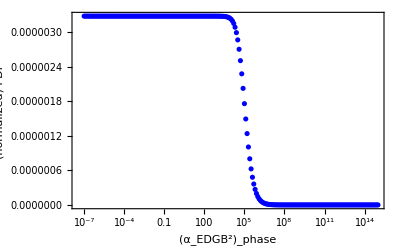

```mathematica
plotαFinalPDFcombLogNorm=ListLogLinearPlot[{αFinalPDFPcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFcombInterpLogNorm=Interpolation[αFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFcombNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFcombInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}]
```

{{0,0},{1.×10^-7,3.27842×10^-13},{1.25893×10^-7,4.12728×10^-13},{1.58489×10^-7,5.19594×10^-13},{1.99526×10^-7,6.5413×10^-13},{2.51189×10^-7,8.23501×10^-13},{3.16228×10^-7,1.03673×10^-12},{3.98107×10^-7,1.30516×10^-12},{5.01187×10^-7,1.6431×10^-12},{6.30957×10^-7,2.06854×10^-12},{7.94328×10^-7,2.60414×10^-12},{1.×10^-6,3.27842×10^-12},{1.25893×10^-6,4.12728×10^-12},{1.58489×10^-6,5.19594×10^-12},{1.99526×10^-6,6.5413×10^-12},{2.51189×10^-6,8.23501×10^-12},{3.16228×10^-6,1.03673×10^-11},{3.98107×10^-6,1.30516×10^-11},{5.01187×10^-6,1.6431×10^-11},{6.30957×10^-6,2.06854×10^-11},{7.94328×10^-6,2.60414×10^-11},{0.00001,3.27842×10^-11},{0.0000125893,4.12728×10^-11},{0.0000158489,5.19594×10^-11},{0.0000199526,6.5413×10^-11},{0.0000251189,8.23501×10^-11},{0.0000316228,1.03673×10^-10},{0.0000398107,1.30516×10^-10},{0.0000501187,1.6431×10^-10},{0.0000630957,2.06854×10^-10},{0.0000794328,2.60414×10^-10},{0.0001,3.27842×10^-10},{0.000125893,4.12728×10^-10},{0.000158489,5.19594×10^-10},{0.000199526,6.5413×10^-10},{0.000251189,8.23501×10^-10},{0.000316228,1.03673×10^-9},{0.000398107,1.30516×10^-9},{0.000501187,1.6431×10^-9},{0.000630957,2.06854×10^-9},{0.000794328,2.60414×10^-9},{0.001,3.27842×10^-9},{0.00125893,4.12728×10^-9},{0.00158489,5.19594×10^-9},{0.00199526,6.5413×10^-9},{0.00251189,8.23501×10^-9},{0.00316228,1.03673×10^-8},{0.00398107,1.30516×10^-8},{0.00501187,1.6431×10^-8},{0.00630957,2.06854×10^-8},{0.00794328,2.60414×10^-8},{0.01,3.27842×10^-8},{0.0125893,4.12728×10^-8},{0.0158489,5.19594×10^-8},{0.0199526,6.5413×10^-8},{0.0251189,8.23501×10^-8},{0.0316228,1.03673×10^-7},{0.0398107,1.30516×10^-7},{0.0501187,1.6431×10^-7},{0.0630957,2.06854×10^-7},{0.0794328,2.60414×10^-7},{0.1,3.27842×10^-7},{0.125893,4.12728×10^-7},{0.158489,5.19594×10^-7},{0.199526,6.5413×10^-7},{0.251189,8.23501×10^-7},{0.316228,1.03673×10^-6},{0.398107,1.30516×10^-6},{0.501187,1.6431×10^-6},{0.630957,2.06854×10^-6},{0.794328,2.60414×10^-6},{1.,3.27842×10^-6},{1.25893,4.12728×10^-6},{1.58489,5.19594×10^-6},{1.99526,6.5413×10^-6},{2.51189,8.23501×10^-6},{3.16228,0.0000103673},{3.98107,0.0000130516},{5.01187,0.000016431},{6.30957,0.0000206854},{7.94328,0.0000260414},{10.,0.0000327842},{12.5893,0.0000412728},{15.8489,0.0000519594},{19.9526,0.000065413},{25.1189,0.0000823501},{31.6228,0.000103673},{39.8107,0.000130516},{50.1187,0.00016431},{63.0957,0.000206854},{79.4328,0.000260414},{100.,0.000327842},{125.893,0.000412728},{158.489,0.000519593},{199.526,0.000654129},{251.189,0.000823498},{316.228,0.00103672},{398.107,0.00130515},{501.187,0.00164308},{630.957,0.0020685},{794.328,0.00260405},{1000.,0.00327823},{1258.93,0.00412691},{1584.89,0.00519521},{1995.26,0.00653984},{2511.89,0.00823209},{3162.28,0.0103614},{3981.07,0.01304},{5011.87,0.0164079},{6309.57,0.0206394},{7943.28,0.02595},{10000.,0.0326033},{12589.3,0.0409162},{15848.9,0.051261},{19952.6,0.0640586},{25118.9,0.0797596},{31622.8,0.0988109},{39810.7,0.121609},{50118.7,0.148445},{63095.7,0.179446},{79432.8,0.214522},{100000.,0.253325},{125893.,0.295267},{158489.,0.339574},{199526.,0.385362},{251189.,0.431709},{316228.,0.477716},{398107.,0.522558},{501187.,0.565532},{630957.,0.606102},{794328.,0.643928},{1.×10^6,0.678853},{1.25893×10^6,0.710859},{1.58489×10^6,0.740027},{1.99526×10^6,0.7665},{2.51189×10^6,0.79046},{3.16228×10^6,0.812109},{3.98107×10^6,0.831657},{5.01187×10^6,0.849306},{6.30957×10^6,0.865235},{7.94328×10^6,0.879605},{1.×10^7,0.892555},{1.25893×10^7,0.90421},{1.58489×10^7,0.914682},{1.99526×10^7,0.924068},{2.51189×10^7,0.93246},{3.16228×10^7,0.939946},{3.98107×10^7,0.946611},{5.01187×10^7,0.952542},{6.30957×10^7,0.95782},{7.94328×10^7,0.96252},{1.×10^8,0.966711},{1.25893×10^8,0.970449},{1.58489×10^8,0.973783},{1.99526×10^8,0.976754},{2.51189×10^8,0.979397},{3.16228×10^8,0.981742},{3.98107×10^8,0.983813},{5.01187×10^8,0.985634},{6.30957×10^8,0.98723},{7.94328×10^8,0.988625},{1.×10^9,0.989843},{1.25893×10^9,0.990911},{1.58489×10^9,0.99185},{1.99526×10^9,0.992678},{2.51189×10^9,0.993411},{3.16228×10^9,0.994061},{3.98107×10^9,0.994637},{5.01187×10^9,0.99515},{6.30957×10^9,0.99561},{7.94328×10^9,0.996027},{1.×10^10,0.996409},{1.25893×10^10,0.996764},{1.58489×10^10,0.997095},{1.99526×10^10,0.997404},{2.51189×10^10,0.99769},{3.16228×10^10,0.997953},{3.98107×10^10,0.998191},{5.01187×10^10,0.998402},{6.30957×10^10,0.998588},{7.94328×10^10,0.998748},{1.×10^11,0.998885},{1.25893×10^11,0.999002},{1.58489×10^11,0.999102},{1.99526×10^11,0.999191},{2.51189×10^11,0.999272},{3.16228×10^11,0.999346},{3.98107×10^11,0.999417},{5.01187×10^11,0.999483},{6.30957×10^11,0.999545},{7.94328×10^11,0.999602},{1.×10^12,0.999655},{1.25893×10^12,0.999703},{1.58489×10^12,0.999745},{1.99526×10^12,0.999782},{2.51189×10^12,0.999814},{3.16228×10^12,0.999841},{3.98107×10^12,0.999863},{5.01187×10^12,0.99988},{6.30957×10^12,0.999894},{7.94328×10^12,0.999905},{1.×10^13,0.999914},{1.25893×10^13,0.999921},{1.58489×10^13,0.999927},{1.99526×10^13,0.999933},{2.51189×10^13,0.99994},{3.16228×10^13,0.999947},{3.98107×10^13,0.999955},{5.01187×10^13,0.999963},{6.30957×10^13,0.999972},{7.94328×10^13,0.99998},{1.×10^14,0.999987},{1.25893×10^14,0.999992},{1.58489×10^14,0.999996},{1.99526×10^14,0.999998},{2.51189×10^14,1.},{3.16228×10^14,1.},{3.98107×10^14,1.},{5.01187×10^14,1.},{6.30957×10^14,1.},{7.94328×10^14,1.},{1.×10^15,1.}}

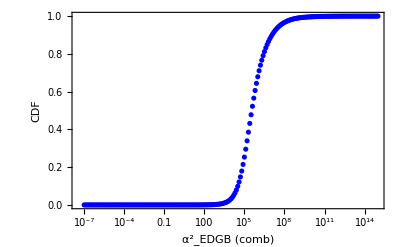

```mathematica
ListLogLinearPlot[αFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (comb)","CDF"}]
```

```mathematica
αFinalCDFcombNormInterp=Interpolation[αFinalCDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
αSquared90CLcomb=x/.FindRoot[αFinalCDFcombNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

1.15425×10^7

```mathematica
√√αSquared90CLcomb//N
```

58.2874

```mathematica
(20.9-26.5)/26.5
```

-0.211321

```mathematica
(57-80)/80//N
```

-0.2875